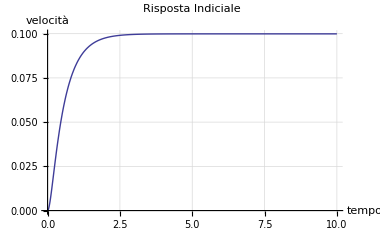

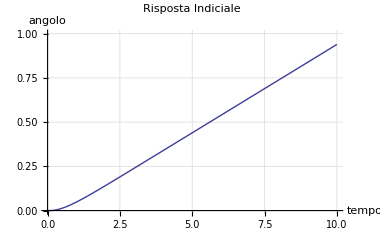

```mathematica
kt = 0.01;
kb = 0.01;
J = 0.01;
B = 0.1;
Lm = 0.5;
Rm = 1;

P1=TransferFunctionModel[1/(Lm s + Rm), s];
P2 = TransferFunctionModel[1/(J s + B), s];
P3 = TransferFunctionModel[kt, s];
Gcd = SystemsModelSeriesConnect[P3, SystemsModelSeriesConnect[P2, P1]];//Simplify
Gcc = SystemsModelFeedbackConnect[Gcd, TransferFunctionModel[kb, s]];//Simplify
Gca = SystemsModelSeriesConnect[Gcc, TransferFunctionModel[1/s, s]];//Simplify

yvind = OutputResponse[Gcc,UnitStep[t],{t, 10}];
yaind = OutputResponse[Gca,UnitStep[t],{t, 10}];

pl1 = Plot[yvind, {t,0,10}, PlotRange->{0, 0.1}, AxesLabel->{"tempo", "velocità"},PlotLabel->"Risposta Indiciale", GridLines->Automatic]
pl2 = Plot[yaind , {t,0,10}, PlotRange->{0, 1.0}, AxesLabel->{"tempo", "angolo"}, PlotLabel->"Risposta Indiciale", GridLines->Automatic]
```

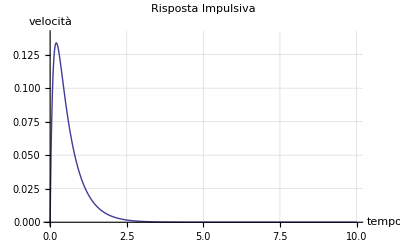

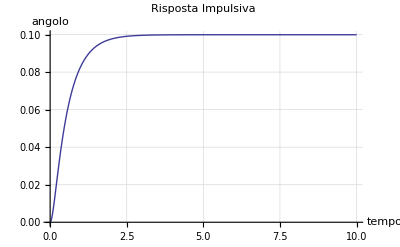

```mathematica
yvind = OutputResponse[Gcc,DiracDelta[t],{t, 10}];
yaind = OutputResponse[Gca,DiracDelta[t],{t, 10}];

pl1 = Plot[yvind, {t,0,10}, PlotRange->{0, 0.14}, AxesLabel->{"tempo", "velocità"}, PlotLabel->"Risposta Impulsiva", GridLines->Automatic]
pl2 = Plot[yaind , {t,0,10}, PlotRange->{0, 0.1}, AxesLabel->{"tempo", "angolo"}, PlotLabel->"Risposta Impulsiva", GridLines->Automatic]
```